## Exercise 3 : the evolution of local adaptation

```mathematica
Clear["Global`*"]
```

### Mean matrix

```mathematica
θ1 =- 1 ; 
θ2 =1 ; 
σ1 =  σ ;
σ2 = σ ;
```

```mathematica
w11 = (1-m)Exp[-((y-θ1)/σ1)^2]/Exp[-((x-θ1)/σ1)^2] ;
w21 = m Exp[-((y-θ1)/σ1)^2]/Exp[-((x-θ1)/σ1)^2] ;
w22 = (1-m)Exp[-((y-θ2)/σ2)^2]/Exp[-((x-θ2)/σ2)^2] ; 
w12 = m Exp[-((y-θ2)/σ2)^2]/Exp[-((x-θ2)/σ2)^2] ;
```

```mathematica
W  = {{w11,w12},{w21,w22}} ; 
W//MatrixForm
```

(ⅇ^((1+x)^2/σ^2-(1+y)^2/σ^2) (1-m) | ⅇ^((-1+x)^2/σ^2-(-1+y)^2/σ^2) m
ⅇ^((1+x)^2/σ^2-(1+y)^2/σ^2) m | ⅇ^((-1+x)^2/σ^2-(-1+y)^2/σ^2) (1-m))

### Eigenvectors of the neutral matrix

```mathematica
W0 = W /.y-> x
```

{{1-m,m},{m,1-m}}

```mathematica
(* class reproductive values *)
v0 = Eigenvectors[Transpose[W0]][[1]]
```

{1,1}

```mathematica
(* class distribution under neutrality  *)
q0 = Eigenvectors[W0][[1]] ; 
q0 = q0 /Total[q0]//Simplify
```

{1/2,1/2}

```mathematica
(* sanity checks *)
v0.q0 == 1 //Simplify
v0 ==  v0.W0 //Simplify
q0 == W0.q0 //Simplify
```

True

True

True

### Selection gradient, singular point and convergence stability

```mathematica
S = v0.(D[W,y]/.y->x).q0  //Simplify
```

-(2 x)/σ^2

```mathematica
sing = Flatten@Solve[S ==0,x]
```

{x→0}

```mathematica
J = D[S,x] /.sing
```

-2/σ^2

### Hessian

```mathematica
(* perturbation of q, this we give to them *)
Eigenvectors[W][[2]]  ;
q1 = q1 /Total[q1]  ;
q1 = Assuming[σ>0&& 0<m<1 && x∈Reals &&y∈Reals,Simplify[q1]]  ;
q1 == q0 /. y-> x   ;
Assuming[σ>0&& 0<m<1 && x∈Reals &&y∈Reals,Simplify[%]] 

(D[q1,y]/.y->x)  ;

% ==1/σ^2{ (2m -1)/(2 m),(1-2 m)/(2 m) };

Assuming[σ>0&& 0<m<1 && x∈Reals &&y∈Reals,FullSimplify[%]]
```

True

True

```mathematica
Dq=1/σ^2{ (2m -1)/(2 m),(1-2 m)/(2 m) } ;
```

#### Hq

```mathematica
v0.(D[W,y]/.y->x).Dq /. y-> x ;
%  /.sing   ; 
Hq =Assuming[σ>0&& 0<m<1 && x∈Reals &&y∈Reals,FullSimplify[%]]
```

(2-4 m)/(m σ^4)

#### Hw

```mathematica
v0.(D[W,y,y]/.y->x).q0   /. y-> x ;
Hw = %  /.sing  //Simplify
```

(4-2 σ^2)/σ^4

#### Evolutionary branching

(4-2 m (2+σ^2))/(m σ^4)

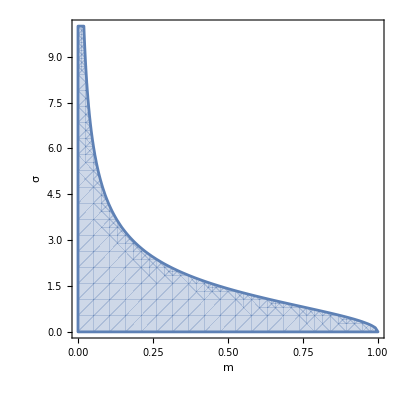

```mathematica
H = Hw+2Hq //Simplify
RegionPlot[H > 0  ,{m,0,1},{σ,0,10},FrameLabel->Automatic]
```

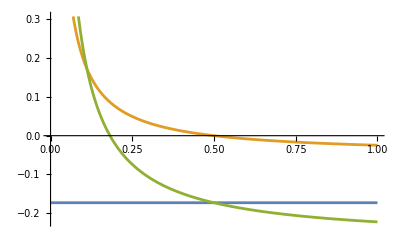

```mathematica
(* when disruptive selection is weak *)
Plot[Evaluate[{Hw,Hq,Hw+2Hq} /. σ->3],{m,0,1}]
```

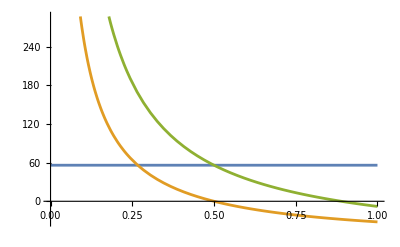

```mathematica
(* when disruptive selection is strong *)
Plot[Evaluate[{Hw,Hq,Hw+2Hq} /. σ->0.5],{m,0,1}]
```

## Exercise 4 : the emergence of life - history polymorphism

```mathematica
Clear["Global`*"]
```

### Leslie Matrix

```mathematica
b1 =k[x] f1 y/x  /. k[x]->  1/(f1+f2-f2 x) ;
b2 =k[x] f2 (1-y)/(1-x)  /. k[x]->  1/(f1+f2-f2 x);
s1=1-y ;
```

```mathematica
L = {{b1,b2},{s1,0}}  ;
```

### Resident population

```mathematica
L0 = L   /.y->x  //Simplify ;
```

```mathematica
Eigenvalues[L0 ]
```

{(f2 (-1+x))/(f1+f2-f2 x),1}

### Current (Fisher’s) reproductive value, survival till, and selection gradient

```mathematica
(* reproductive value *)
v0 = Eigenvectors[Transpose[L0]][[2]] //Simplify ;
(* normalised such that v0[[1]] == 1 *) 
v0 = v0/v0[[1]]//Simplify
v0 == v0.L0 //Simplify
```

{1,f2/(f1+f2-f2 x)}

True

```mathematica
(* survival till under neutality *)
l0 = {1,s1}  /.y->x  ;
```

```mathematica
S = (D[b1,y]+v0[[2]]D[s1,y])l0[[1]] +  D[b2,y]  l0[[2]]  /.y->x  //Simplify
```

(f1-2 f2 x)/(x (f1+f2-f2 x))

```mathematica
equi = Flatten@Solve[% == 0,x]
```

{x→f1/(2 f2)}

```mathematica
J = D[S,x]    /. equi //Simplify
```

-(8 f2^2)/(f1^2+2 f1 f2)

### Hessian

```mathematica
(* survival till under selection *)
l = {1,s1}   ;
```

```mathematica
Hw = (D[b1,y,y]+v0[[2]]D[s1,y,y])l0[[1]]+  D[b2,y,y]  l0[[2]] /.y->x  /. equi //Simplify
Hq = (D[b1,y]+v0[[2]]D[s1,y])*D[l[[1]],y] +  D[b2,y]  D[l[[2]],y] /.y->x  /. equi //Simplify
```

0

-(4 f2^2)/(f1^2-4 f2^2)

```mathematica
H = Hw + 2 Hq  //Simplify
```

-(8 f2^2)/(f1^2-4 f2^2)

```mathematica
(* conditions for evolutionary branching *)
Reduce[J<0 &&H>0 && f2>0 &&f1> 0]
```

f2>0&&f1>2 f2

i . e . branching occurs when fecundity at age 1 is large enough compared to fecundity at age 2, which makes it possible for individuals to specialise for reproduction at age 1 and others at age 2. This is because the trait not only allows for individual to be more fecund in one age class, it also associates with that age class.